```mathematica
Decomposicao de um tensor
```

de Decomposicao tensor um

```mathematica
Young=100;
Poisson=0.25;
lambda=(Poisson*Young)/((1+Poisson)*(1-2 Poisson));
mu=Young/(2(1+Poisson));
(*G=(Young)/(2*(1+Poisson));*)
Kk=(Young)/(3*(1-2Poisson));
Sigma[Eelastico_]:=lambda Tr[Eelastico]IdentityMatrix[3]+2 mu Eelastico;
ComputeStrain[sigma_]:=1/(9K)Tr[sigma]IdentityMatrix[3]+1/(2G)s[sigma];
s[sigma_]:=sigma-(1/3 Tr[sigma] IdentityMatrix[Length[sigma]]);
i1[sigma_]:=Tr[sigma]; 
j2[sigma_]:=1/2 Tr[s[sigma].s[sigma]];
Spectrum[sigma_]:=Block[{i,xy,xz,yz,val2,J3,J2,x1a,x2a,x3a,theta,eigenval,eigenvec,I1,I3,I2,e1,e2,e3,S,temp,j,Q,R,x1,x2,x3,val,X,eigensis,a,b,c,size},
size=Length[sigma];
eigenval=Eigenvalues[sigma];
eigenvec=Eigenvectors[sigma];
eigensis=Eigensystem[sigma];
(*Print["sigma = ",sigma];
Print["eigenval = ",eigenval];
Print["eigenvec = ",eigenvec];*)
I1=Tr[sigma]; 
I2=1/2(Tr[sigma]^2-Tr[sigma.sigma]); 
I3=Det[sigma];

(*Print["I1 = ",I1];
Print["I2 = ",I2];
Print["I3 = ",I3];*)
R=(-2 I1^3+9I1 I2-27 I3)/54.;
(*Print["R = ",R];*)
Q=(I1^2-3 I2)/9.;

If[Q<1*10^-15,Q=1*10^-15];
val=R/(√(Q^3));

If[Abs[val]<1,
theta=ArcCos[val];
];

If[val≥ 1,
theta=0;
];
If[val≤ - 1,
theta=Pi;
];

x1=-2 √Q Cos[theta/3]+I1/3;
x2=-2 √Q Cos[(theta+2Pi)/3]+I1/3;
x3=-2 √Q Cos[(theta-2Pi)/3]+I1/3;

If[x1< x2,temp=x1; x1=x2;x2=temp;];
If[x2< x3,temp=x2; x2=x3;x3=temp;];
If[(x2-x3<1*10^-5)&& (x1-x2≥ 10^-5) , 

(*Print["x1≠ x2 && x2==x3"];*)

e1=(x1/(2 x1^3-I1 x1^2+I3)(sigma.sigma-(I1-x1)sigma+I3/x1 IdentityMatrix[size]));
e2=IdentityMatrix[size]-e1;
e3=IdentityMatrix[size] 0;


(*Print["e1 = ",e1//MatrixForm];
Print["e2 = ",e2//MatrixForm];
Print["e3 = ",e3//MatrixForm];*)

Return[{x1,x2,x3,e1,e2,e3}];

,If[(x1-x2)<10^-5 && (x2-x3)≥ 10^-5,
(*Print["x1= x2 && x2!=x3"];*)
e3=x3/(2 x3^3-I1 x3^2+I3)(sigma.sigma-(I1-x3)sigma+I3/x3 IdentityMatrix[size]);

e2=IdentityMatrix[size]-e3;
e1=IdentityMatrix[size] 0;


Return[{x1,x2,x3,e1,e2,e3}];

,If[x1-x2<1*10^-5&& x2-x3<1*10^-5,

(*Print[" x1 == x2 && x2 == x3"];*)

e1=IdentityMatrix[size] ;
e2=IdentityMatrix[size] 0;
e3=IdentityMatrix[size] 0;
Return[{x1,x2,x3,e1,e2,e3}];

,

(*If[x1≠ x2 && x2≠ x3 ,*)

(*Print[" x1 != x2 && x2 != x3"];*)

e1=x1/(2 x1^3-I1 x1^2+I3)(sigma.sigma-(I1-x1)sigma+I3/x1 IdentityMatrix[3]);
e2=x2/(2 x2^3-I1 x2^2+I3)(sigma.sigma-(I1-x2)sigma+I3/x2 IdentityMatrix[3]);
e3=x3/(2 x3^3-I1 x3^2+I3)(sigma.sigma-(I1-x3)sigma+I3/x3 IdentityMatrix[3]);
Return[{x1,x2,x3,e1,e2,e3}]

(*];*)
]
]
]

];
```

```mathematica
Funcoes de Sandler Dimaggio PV
```

de Dimaggio Funcoes PV Sandler

```mathematica
Plot[FF[I1,0]/.subst,{I1,-2,0.1}]
```

ReplaceAll::reps: {subst} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

```mathematica
flag=True;
flag2=True;(*If True bate com philippe e ψ deve ser = 1 para bater*)
subst = {D->  0.67,R-> 2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->1,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
FF[x_,ϕ_]:=A-C Exp[x B]-ϕ x;
s[sigma_]:=sigma-1/3 Tr[sigma]IdentityMatrix[3];
T[ξ_,ρ_,β_]:=Block[{sig1,sig2,sig3},
sig1=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ )Cos[β];
sig2=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ   )Cos[β-2Pi/3];
sig3=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ  )Cos[β+2Pi/3];

(*sig1=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ )Sin[β-2Pi/3];
sig2=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ   )Sin[β];
sig3=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ  )Sin[β+2Pi/3];*)

Return[{sig1,sig2,sig3}];
]
(* Ponto de F1 no espaco Haigh Westergaard coordenadas cylindricas *)
F1HWCyl[ξ_,β_]:=Block[{A,B,C,W,ψ,NN,ϕ,Γ,I1,sqrtj2,ρ,sig1,sig2,sig3},
Γ=1/2(1+Sin[3 β]+1/ψ(1-Sin[3 β]));
FF[I1_,ϕ_]:=A-C Exp[I1 B]-ϕ I1;
I1=ξ Sqrt[3];
sqrtj2=(FF[I1,ϕ]-NN)/ Γ;
ρ=Sqrt[2]sqrtj2;
(*ξ=I1/Sqrt[3];*)
Return[{ξ,ρ,β}];
]
(* Ponto de F1 no espaco Haigh Westergaard *)
(* Diogo - nao tenho certeza que eh cos[beta] sin[beta] *)
F1HWCart[ξ_,β_]:=Block[{temp},
temp=F1HWCyl[ξ,β];
{temp[[1]],Cos[temp[[3]]]temp[[2]],Sin[temp[[3]]]temp[[2]]}
]
(* Ponto de F1 no espaco de tensoes principais *)
F1[ξ_,β_]:=Block[{FHW},
FHW=F1HWCyl[ξ,β];
Return[T[FHW[[1]],FHW[[2]],FHW[[3]]]];
]
F2HWCyl[θ_,β_,L_]:=Block[{R,A,B,C,W,ψ,NN,ϕ,Γ,I1,sqrtj2,ρ,sig1,sig2,sig3,ξ},
Γ=1/2(1+Sin[3 β]+1/ψ(1-Sin[3 β]));
(*sqrtj2=((FF[L,ϕ]-NN)/Γ)Cos[θ];*)
sqrtj2=(FF[L,ϕ]-NN)Sin[θ]/Γ;
(*I1=R FF[L,ϕ]Sin[θ]+L;*)
If[flag==True,
I1=L-R FF[L,ϕ]Cos[θ];
sqrtj2=(FF[L,ϕ]-NN)Sin[θ]/Γ;
,
I1=L-R FF[L,ϕ]Sin[θ];
sqrtj2=(FF[L,ϕ]-NN)Cos[θ]/Γ;
];
If[flag2==True,(*bate com philippe*)
I1=L+R FF[L,ϕ]Cos[θ];
sqrtj2=(FF[L,ϕ]-NN)Sin[θ]/Γ;
(*I1=L+R ff[L,ϕ]Cos[θ];
sqrtj2=(ff[L,ϕ]-NN)Sin[θ]/Γ[β];*)

];
ξ=I1/Sqrt[3];
ρ=sqrtj2 Sqrt[2];
Return[{ξ,ρ,β}];
]
F2HWCart[θ_,β_,L_]:=Block[{temp},
temp=F2HWCyl[θ,β,L];
{temp[[1]],Cos[temp[[3]]]temp[[2]],Sin[temp[[3]]]temp[[2]]}
]
F2[θ_,β_,L_]:=Block[{FHW},
FHW=F2HWCyl[θ,β,L];
Return[T[FHW[[1]],FHW[[2]],FHW[[3]]]];
]

DistFunc1[pt_,ξ_,β_]:=Block[{parametrictrial,parametric,x,p1,y,p2,z,p3,distf1,sig,sigtrial,sigHW,sig2,sig3,sig1tr,sig2tr,sig3tr,haigh,haightrial,G,K,Rot},
Rot=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
(*parametriza os pontos das coordenadas {ξ,ρ,β} para {ξ,θ,β}*)
parametric=F1HWCart[ξ,β];
(*Matriz de rotacao que parametriza os pontos das coordenadas {σ1,σ2,σ3} para {ξ,θ,β}*)
parametrictrial=Rot.pt;


distf1=Sqrt[1/(3 K)(parametrictrial[[1]]-parametric[[1]])^2 +1/(2G)((parametrictrial[[2]]-parametric[[2]])^2 +(parametrictrial[[3]]-parametric[[3]])^2)];
Return[distf1]
];
DistFunc2[pt_,θ_,β_,L_]:=Block[{parametrictrial,parametric,distf2,haigh,haightrial,G,K,Rot},

Rot=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
(*parametriza os pontos das coordenadas {ξ,ρ,β} para {ξ,θ,β}*)
parametric=F2HWCart[θ,β,L];
(*Matriz de rotacao que parametriza os pontos das coordenadas {σ1,σ2,σ3} para {ξ,θ,β}*)
parametrictrial=Rot.pt;
distf2=Sqrt[1/(3 K)(parametrictrial[[1]]-parametric[[1]])^2 +1/(2G)((parametrictrial[[2]]-parametric[[2]])^2 +(parametrictrial[[3]]-parametric[[3]])^2)];
Return[distf2]
];
```

```mathematica
Transformacoes
```

Transformacoes

```mathematica
FromHWCylToHWCart[vec_]:=Block[{sig2tiu,sig3tiu,ξ,ρ,β},
ξ=vec[[1]];
ρ=vec[[2]];
β=vec[[3]];
sig2tiu=ρ Cos[β];
sig3tiu=ρ Sin[β];
{ξ,sig2tiu,sig3tiu}
];
FromHWCartToHWCyl[vec_]:=Block[{ρ,β,ξ,sig2tiu,sig3tiu},
ξ=vec[[1]];
sig2tiu=vec[[2]];
sig3tiu=vec[[3]];
ρ=Sqrt[sig2tiu^2+sig3tiu^2];
β=ArcTan[sig2tiu,sig3tiu];
{ξ,ρ,β}
];
FromHWCylToPrincipal[vec_]:=Block[{sig1,sig2,sig3,ξ,ρ,β},
ξ=vec[[1]];
ρ=vec[[2]];
β=vec[[3]];
sig1=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ )Cos[β];
sig2=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ   )Cos[β-2Pi/3];
sig3=(1/Sqrt[3])ξ+(Sqrt[2/3]ρ  )Cos[β+2Pi/3];
{sig1,sig2,sig3}
];
FromPrincipalToHWCyl[vec_]:=Block[{ROT,ξ,ρ,β,sig2tiu,sig3tiu,inter},
ROT=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
inter=(ROT.vec);
ξ=inter[[1]];
sig2tiu=inter[[2]];

sig3tiu=inter[[3]];

ρ=Sqrt[sig2tiu^2+sig3tiu^2];
β=ArcTan[sig2tiu,sig3tiu];
{ξ,ρ,β}
];
FromPrincipalToHWCart[vec_]:=Block[{ROT,ξ,ρ,β,sig2tiu,sig3tiu,inter},
ROT=({{1/(√3), 1/(√3), 1/(√3)}, {√(2/3), -1/(√6), -1/(√6)}, {0, 1/(√2), -1/(√2)}});
inter=(ROT.vec);
ξ=inter[[1]];
sig2tiu=inter[[2]];
sig3tiu=inter[[3]];
{ξ,sig2tiu,sig3tiu}
];
```

```mathematica
Derivadas
```

Derivadas

```mathematica
EpsEqX[X_]:=W E^(D X)(*phil mexeu *)
XEqL[L_]:=L-R FF[L,ϕ]
EpsEqL[L_]:=EpsEqX[XEqL[L]]
ResL[pt_,θ_,β_,L_,Lprev_]:=Block[{resl,haigh,haightrial,G,K,Rot,depspdl,A,R,B,W,d,I1,I1tr,ϕ,δL,l,L0,delepsp},

I1tr=pt[[1]]+pt[[2]]+pt[[3]];
I1=R FF[L,ϕ]Cos[θ]+L;
delepsp=EpsEqL[L]-EpsEqL[Lprev];
resl=3K delepsp- (I1tr-I1);
Return[resl]
];
DDistFunc1[pt_,ξ_,β_]:=Block[{a,b,res},
res={D[DistFunc1[pt,a,b]^2,a],D[DistFunc1[pt,a,b]^2,b]}/.{a->ξ,b->β};
res
]
D2DistFunc1[pt_,ξ_,β_]:=Block[{res,a,b},
res={{D[DistFunc1[pt,a,b]^2,a,a],D[DistFunc1[pt,a,b]^2,a,b]},
{D[DistFunc1[pt,a,b]^2,b,a],D[DistFunc1[pt,a,b]^2,b,b]}}/.{a->ξ,b->β};
res
]
DDistFunc2[pt_,θ_,β_,L_,Lprev_]:=Block[{a,b,c,res},
res={D[DistFunc2[pt,a,b,c]^2,a],D[DistFunc2[pt,a,b,c]^2,b],ResL[pt,a,b,c,Lprev]}/.{a->θ,b->β,c->L};
res
]
D2DistFunc2[pt_,θ_,β_,L_,Lprev_]:=Block[{res,a,b,c},
res={{D[DistFunc2[pt,a,b,c]^2,a,a],D[DistFunc2[pt,a,b,c]^2,a,b],D[DistFunc2[pt,a,b,c]^2,a,c]},
{D[DistFunc2[pt,a,b,c]^2,b,a],D[DistFunc2[pt,a,b,c]^2,b,b],D[DistFunc2[pt,a,b,c]^2,b,c]},
{D[ResL[pt,a,b,c,Lprev],a],D[ResL[pt,a,b,c,Lprev],b],D[ResL[pt,a,b,c,Lprev],c]}}/.{a->θ,b->β,c->L};
res
]
```

```mathematica
Algoritimos de projecao
```

Algoritimos de projecao

{0.116452,2.89903}

3 D ⅇ^(D (L-R (A-C ⅇ^(B L)-L ϕ))) K W (1-R (-B C ⅇ^(B L)-ϕ))

0.1+200. (-0.0658213+0.066 ⅇ^(0.67 (-2.5 (0.25-0.18 ⅇ^(0.67 L))+L)))

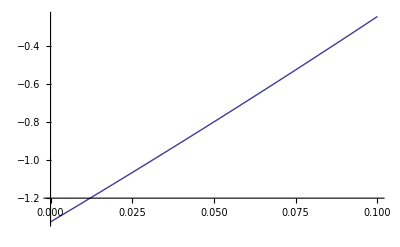

8.844 ⅇ^(0.67 (-2.5 (0.25-0.18 ⅇ^(0.67 L))+L)) (1+0.3015 ⅇ^(0.67 L))

```mathematica
MinF1[pt_]:=Block[{ϕ,distf1,resf1,jac11,jac12,jac21,jac22,sig1,sig2,sig3,ξ,β,ξn1,ξn,df1dxi,df1dbeta,βn1,βn,i,j,res,jac,resn,resn1,resnorm,counter,
chute,temp,I1,sol,f1,ptmin,xiguess,beta,distxi,distnew,betaguess},
resvec1={};
res=DDistFunc1[pt,ξ,β];
jac=D2DistFunc1[pt,ξ,β];
distxi=10^8;
βn=Pi;
For[xiguess=-Pi,xiguess≤Pi,xiguess+=Pi/20,
For[betaguess=0,betaguess<=2 Pi,betaguess+=Pi/20,
distnew=DistFunc1[pt,xiguess,betaguess]/.subst;
If[Abs[distnew]<Abs[distxi],
ξn=xiguess;
βn=betaguess;
distxi=distnew;
];
];
];

resnorm=1;
counter=1;
resvec1={};
While[(resnorm>10^-12&&counter<30),
{ξn1,βn1}={ξn,βn}-Inverse[jac/.{ξ->ξn,β->βn}/.subst].(res/.{ξ->ξn,β->βn}/.subst);
resnorm=Norm[{ξn1,βn1}-{ξn,βn}];
(*Print["resnorm = ",resnorm];*)
AppendTo[resvec1,resnorm];
{ξn,βn}={ξn1,βn1};
counter++;
];
(*Print["resnorm = ",resnorm];*)
Return[{ξn,βn}]
];
MinF2[pt_,Lprev_]:=Block[{distf1,resf1,jac11,jac12,jac21,jac22,sig1,sig2,sig3,θ,L,θn,β,ξn1,ξn,df1dxi,df1dbeta,βn1,βn,
i,j,res,jac,resn,resn1,resnorm,counter,Ln,chute,θn1,temp,L0,Ln1,deltal,thetaguess,distnew,disttheta,betaguess},
res=DDistFunc2[pt,θ,β,L,Lprev];
jac=D2DistFunc2[pt,θ,β,L,Lprev];

disttheta=10^8;
βn=Pi;
For[thetaguess=0,thetaguess≤Pi,thetaguess+=Pi/20,
For[betaguess=0,betaguess<=2 Pi,betaguess+=Pi/20,
distnew=DistFunc2[pt,thetaguess,betaguess,Lprev]/.subst;
If[Abs[distnew]<Abs[disttheta],
θn=thetaguess;
βn=betaguess;
disttheta=distnew;

];
];
];


Ln=Lprev;
resnorm=1;
counter=1;
resvec2={};
invjac=Inverse[jac/.{θ->θn,β->βn,L->Ln}/.subst];
deltal=0;
While[(resnorm>10^-12&&counter<30),
{θn1,βn1,Ln1}={θn,βn,Ln}-Inverse[jac/.{θ->θn,β->βn,L->Ln}/.subst].(res/.{θ->θn,β->βn,L->Ln}/.subst);
(*{θn1,βn1,Ln1}={θn,βn,Ln}-invjac.(res/.{θ->θn,β->βn,L->Ln}/.subst);*)
resnorm=Norm[{θn1,βn1,Ln1}-{θn,βn,Ln}];
(*Print["resnorm = ",resnorm];*)
{θn,βn,Ln}={θn1,βn1,Ln1};
AppendTo[resvec2,resnorm];
counter++;
];

Return[{θn,βn,Ln1-Lprev}]
];
MinF2θconst[pt_,Lprev_]:=Block[{distf1,resf1,jac11,jac12,jac21,jac22,sig1,sig2,sig3,θ,θn,β,ξn1,ξn,df1dxi,df1dbeta,βn1,βn,L,
i,j,res,jac,resn,resn1,resnorm,counter,Ln,chute,θn1,temp,L0,Ln1,deltal,θtr,thetaguess,betaguess,distnew,disttheta,θtr1},
res=DDistFunc2[pt,θ,β,L,Lprev];
jac=D2DistFunc2[pt,θ,β,L,Lprev];
βn=Pi;
θtr1=Pi/2;
For[betaguess=0,betaguess<=2 Pi,betaguess+=Pi/20,
distnew=DistFunc2[pt,Pi/2,betaguess,Lprev]/.subst;
If[Abs[distnew]<Abs[disttheta],
βn=betaguess;
disttheta=distnew;
];
];
θtr=θtr1;
resnorm=1;
counter=1;
resvec2={};
Ln=Lprev;
invjac=Inverse[jac/.{θ->θtr1,β->βn,L->Lprev}/.subst];
deltal=0;
While[(resnorm>10^-12&&counter<30),
{θtr,βn1,Ln1}={θtr1,βn,Ln}-Inverse[jac/.{θ->θtr,β->βn,L->Ln}/.subst].(res/.{θ->θtr,β->βn,L->Ln}/.subst);
(*{θn1,βn1,Ln1}={θn,βn,Ln}-invjac.(res/.{θ->θn,β->βn,L->Ln}/.subst);*)
resnorm=Norm[{θtr1,βn1,Ln1}-{θtr1,βn,Ln}];
Print["resnorm = ",resnorm];
{θtr,βn,Ln}={θtr1,βn1,Ln1};
AppendTo[resvec2,resnorm];
counter++;
];

Return[{θtr,βn,Ln1-Lprev/.subst}]
];
pt={0.01,0.13,0.1};
MinF1[pt]
ResL2[pt_,L0_,I1pr_,I1tr_]:=Block[{resl,haigh,haightrial,G,K,Rot,depspdl,A,R,B,W,d,I1,ϕ,δL,l,L},

delepsp=EpsEqL[L]-EpsEqL[L0];
resl=3K delepsp- (I1tr-I1pr);
Return[resl]
];
D[ResL2[{sig1,sig2,sig3},L0,I1Tr,I1Pr],L]
f=ResL2[pt,0.13,-0.1,-0.2]/.subst
Plot[f,{L,0,0.1}]
D[ResL2[pt,0.13,-0.1,-0.2]/.subst,L]

MinResL[pt_,L0_,I1tr_,I1Pr_]:=Block[{fx,dfx,xn1,xn,i},

fx=ResL2[pt,L0,I1tr,I1Pr];
dfx=D[ResL2[pt,L0,I1tr,I1Pr],L];
fx=fx/.subst;
dfx=dfx/.subst;
xn=L0;
For[i=1,i<10,i++,
xn1=xn-(fx/.L->xn)/(dfx/.L->xn);
xn=xn1;
];
xn
];
```

```mathematica
Atualizacoes e conversoes
```

Atualizacoes conversoes e

```mathematica
UpdateF2Principal[vec_]:=Block[{R,ϕ,I1,sqrtj2,NN,Γ,ψ,xi,rho,beta,sig,θ,β,L},
θ=vec[[1]];
β=vec[[2]];
L=vec[[3]];
Γ=1/2(1+Sin[3 β]+1/ψ(1-Sin[3 β]));
I1=R FF[L,ϕ]Cos[θ]+L;
sqrtj2=(FF[L,ϕ]-NN)Sin[θ]/Γ;
xi=I1/Sqrt[3];
rho=sqrtj2 Sqrt[2];
beta=β;
sig=FromHWCylToPrincipal[{xi,rho,beta}];
Return[sig]
];
UpdateF2[vec_]:=Block[{R,ϕ,I1,sqrtj2,NN,Γ,ψ,xi,rho,beta,sig,θ,β,L},
θ=vec[[1]];
β=vec[[2]];
L=vec[[3]];
Γ=1/2(1+Sin[3 β]+1/ψ(1-Sin[3 β]));
I1=R FF[L,ϕ]Cos[θ]+L;
sqrtj2=(FF[L,ϕ]-NN)Sin[θ]/Γ;
{I1,sqrtj2}/.subst
];
CalcNewSigFroI1J2Beta[vec_]:=Block[{xi,rho,beta,sig},
xi=vec[[1]]/Sqrt[3];
rho=vec[[2]]Sqrt[2];
beta=vec[[3]];
sig=FromHWCylToPrincipal[{xi,rho,beta}];
Return[sig]
];
UpdateF1[vec_]:=Block[{R,ϕ,I1,sqrtj2,NN,Γ,ψ,xi,rho,beta,sig,ξ,β},
ξ=vec[[1]];
β=vec[[2]];
Γ=1/2(1+Sin[3 β]+1/ψ(1-Sin[3 β]));
I1=ξ Sqrt[3];
sqrtj2=(FF[I1,ϕ]-NN)/ Γ;
xi=I1/Sqrt[3];
rho=sqrtj2 Sqrt[2];
beta=β;
(*sig=FromHWCylToPrincipal[{xi,rho,beta}];
Return[sig]*)
{I1,sqrtj2}/.subst
];
UpdateF1Principal[vec_]:=Block[{R,ϕ,I1,sqrtj2,NN,Γ,ψ,xi,rho,beta,sig,ξ,β},
ξ=vec[[1]];
β=vec[[2]];
Γ=1/2(1+Sin[3 β]+1/ψ(1-Sin[3 β]));
I1=ξ Sqrt[3];
sqrtj2=(FF[I1,ϕ]-NN)/ Γ;
xi=I1/Sqrt[3];
rho=sqrtj2 Sqrt[2];
beta=β;
sig=FromHWCylToPrincipal[{xi,rho,beta}];
Return[sig]/.subst
];
CalcNewSig[sig_,vec_]:=Block[{R,ϕ,NN,Γ,ψ,ss,diag,sqrtjj2,ratio},
diag=IdentityMatrix[3](vec[[1]]/3);
sqrtjj2=Sqrt[j2[sig]];
If[sqrtjj2>0,
ratio=vec[[2]]/sqrtjj2;
,
ratio=1;
];
ss=s[sig];
ss*=ratio;
ss+=diag/.subst;
Return[ss]

];
YieldFunction[pt_,k_]:=Block[{principal,cyl,I1,J2,f1,f2,R,ϕ,Γ,sig1,sig2,sig3,xirhobeta,β,ψ},
sig1=pt[[1]];
sig2=pt[[2]];
sig3=pt[[3]];
J2=1/2 ((sig1+1/3 (-sig1-sig2-sig3))^2+(sig2+1/3 (-sig1-sig2-sig3))^2+(1/3 (-sig1-sig2-sig3)+sig3)^2);
I1=sig1+sig2+sig3;
xirhobeta=FromPrincipalToHWCyl[pt];
β=xirhobeta[[3]];
Γ=1/2(1+Sin[3 β]+1/ψ(1-Sin[3 β]));
f1=(Sqrt[J2]-FF[I1/Sqrt[3],ϕ])Γ;
f2=(((I1-k)/(R FF[k,ϕ]))^2+((Γ Sqrt[J2])/FF[k,ϕ])^2-1);
Return[{f1,f2}/.subst]
]
FromSigToI1SqrtJ2[sig_]:=Block[{sig1,sig2,sig3,sqrtJ2,I1},
sig1=sig[[1]];
sig2=sig[[2]];
sig3=sig[[3]];
sqrtJ2=Sqrt[1/2 ((sig1+1/3 (-sig1-sig2-sig3))^2+(sig2+1/3 (-sig1-sig2-sig3))^2+(1/3 (-sig1-sig2-sig3)+sig3)^2)];
I1=sig1+sig2+sig3;
{I1,sqrtJ2}/.subst
];
```

0.28

ParametricPlot3D::plln: Limiting value sol2 in {ξ, sol2, sol1} is not a machine-sized real number.

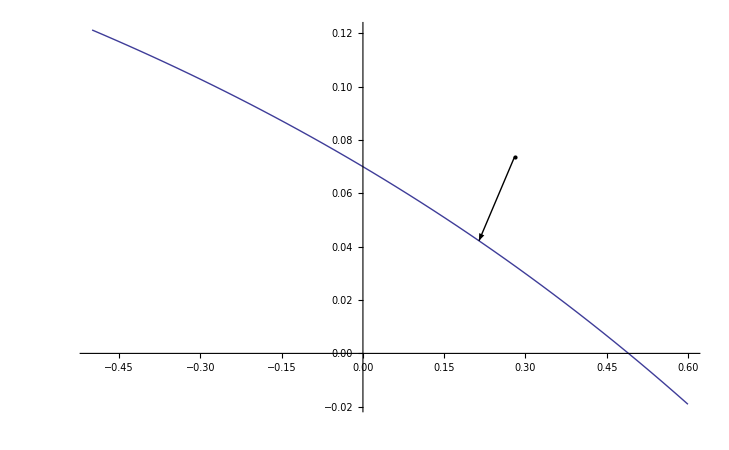

ParametricPlot3D::plln: Limiting value sol2 in {ξ, sol2, sol1} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ParametricPlot3D[F1[ξ, β]/. subst, {ξ, sol2, sol1}, {β, 0, 2 π}], Graphics3DBox[List[], List[Rule[Axes, True], Rule[PlotRange, List[List[0.`, 0.`], List[0.`, 0.`], List[0.`, 0.`]]], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`], Scaled[0.02`]]]]].

Show[ParametricPlot3D[F1[ξ,β]/.subst,{ξ,sol2,sol1},{β,0,2 π}],-Graphics3D-]

```mathematica
pt={0.01,0.15,0.12};
I1=pt[[1]]+pt[[2]]+pt[[3]]
sig1=pt[[1]];
sig2=pt[[2]];
solmin=MinF1[pt];
i1sqrtj2=UpdateF1[solmin]/.subst;
sig3=pt[[3]];
sqrtJ2=Sqrt[1/2 ((sig1+1/3 (-sig1-sig2-sig3))^2+(sig2+1/3 (-sig1-sig2-sig3))^2+(1/3 (-sig1-sig2-sig3)+sig3)^2)];
point=Graphics[Point[{I1,sqrtJ2}]];
vec=Graphics[Arrow[{{I1,sqrtJ2},i1sqrtj2}]];
pl=Plot[FF[I1,0]/.subst,{I1,-0.5,0.6},AxesOrigin->{0,0},PlotRange->All];
plot1=ParametricPlot3D[F1[ξ,β]/.subst,{ξ,sol2,sol1},{β,0,2 Pi}];
plot2=ParametricPlot3D[F2[θ,β]/.subst,{θ,Pi/2.,Pi},{β,0,2 Pi}];
Show[pl,point,vec]
Show[plot1,plot2]
```

```mathematica
FF[i11,0]
```

A-C ⅇ^(B i11)

```mathematica
gerenciamento das funcoes implementadas
```

das funcoes gerenciamento implementadas

```mathematica
ProjectSandlerExtPV[E_,EP_,k_]:=Block[{sqrtJ2,sig1,sig2,sig3,newsig,sqrtdeltaJ2,spc,stress,pt,xirhobeta,yield,I1,ksol,EPnext,Enext,sol,sigsol,deltaI1,deltaS,deltasig,K,G,I1proj,I1sqrtj2,delnewsig},
stress=Sigma[E-EP];
(*spc=Spectrum[stress];*)
spc=Eigenvalues[stress];
(*Print["spc = ",spc];*)
pt={spc[[1]],spc[[2]],spc[[3]]};
(*Print["ktrial = ",k];
Print["sigtrial = ",pt];
Print["yieldtrial = ",YieldFunction[pt,k]];*)
yield=YieldFunction[pt,k];
I1=pt[[1]]+pt[[2]]+pt[[3]];
(*Print["I1trial = ",I1];*)
If[(yield[[2]]≤0 && I1≤k)||(yield[[1]]≤0 && I1>k),
EPnext=EP;
ksol=k;
sigsol=pt;
newsig=stress;
Print["Elastic"];
,

If[(yield[[2]]>0 && I1<k),

(*Print["F2"];*)
sol=MinF2[pt,k];
sol[[3]]+=k;
sigsol=UpdateF2Principal[sol]/.subst;
ksol=sol[[3]];
,
	Print["F1"];
	sol=MinF1[pt];
	sigsol=UpdateF1Principal[sol]/.subst;
	I1proj=sigsol[[1]]+sigsol[[2]]+sigsol[[3]];
	ksol=MinResL[pt,k,I1,I1proj];
	If[ksol>I1proj,
		Print["Ring"];
		sol=MinF2θconst[pt,ksol];
		sol[[3]]+=k;
		sigsol=UpdateF2Principal[sol]/.subst;
		ksol=sol[[3]];
	];

];
(*Print["Plastic"];*)
I1sqrtj2=FromSigToI1SqrtJ2[sigsol];
newsig=CalcNewSig[stress,I1sqrtj2];
delnewsig=stress-newsig;
EPnext=EP+ComputeStrain[delnewsig]/.subst;

];

(*Print["ksol = ",ksol];
Print["sigsol = ",sigsol];
Print["yield = ",YieldFunction[sigsol,ksol]];*)
Return[{newsig,EPnext,ksol}]
];
```

Elastic

Elastic

Elastic

«2 more identical outputs»

F1

F1

F1

«3 more identical outputs»

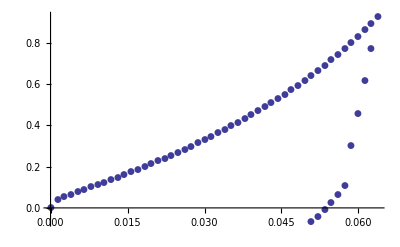

```mathematica
dEps={{-0.0013,0,0},{0,0,0},{0,0,0}};
Eps={{-0.0000001,0,0},{0,0,0},{0,0,0}};
EP={{0,0,0},{0,0,0},{0,0,0}};
k=0.13;
solu={};
sigg={{0,0,0},{0,0,0},{0,0,0}};
For[i=1,i≤60,i++,
(*Print[" i = ",i];*)
soll=ProjectSandlerExtPV[Eps,EP,k];
(*Print[ "soll = ",soll];*)
{sigg,EP,k}=soll;
AppendTo[solu,{-Eps[[1,1]],-sigg[[1,1]]}];
If[i==50,dEps*=-1];
Eps+=dEps;
];
ListPlot[solu,AxesOrigin->{0,0},PlotMarkers->Automatic,PlotRange->All]
```

```mathematica
Projecao sobre Func1
```

Func1 Projecao sobre

```mathematica
pt={0.01,0.13,0.1};
sigma=pt IdentityMatrix[3];
lprev=0.13;
sol=MinF1[pt]
UpdateF1[sol]
v1=Graphics3D[{Arrow[{pt,F1[sol[[1]],sol[[2]]]/.subst}]}];
sol1=FindRoot[{F1[ξ,β]-F2[θ,β,lprev]==0/.subst},{ξ,0},{θ,0},{β,0}][[1]][[2]]
sol2=Solve[((FF[Sqrt[3]ξ,ϕ]-NN)/.subst)==0,ξ][[1]][[1]][[2]]

(*
f1pts=Table[(F1HWCart[ξ/Sqrt[3],β]/.subst),{ξ,sol[[3]]+lprev,Sqrt[3]sol2,0.005},{β,0,2Pi,0.06}];
f2pts=Table[(F2HWCart[θ,β,sol[[3]]+lprev]/.subst),{θ,Pi/2,Pi,0.07},{β,0,2Pi,0.07}];
graph1=Graphics3D[Table[{Blue,Point[{f1pts[[i]]}]},{i,1,Length[f1pts]}]];
graph2=Graphics3D[Table[{Red,Point[{f2pts[[i]]}]},{i,1,Length[f2pts]}]];
Show[v1,graph1,graph2,PlotRange->All];
*)

f3pts=Table[(F1[ξ/Sqrt[3],β]/.subst),{ξ,lprev,Sqrt[3]sol2,0.005},{β,0,2Pi,0.06}];
f4pts=Table[(F2[θ,β,lprev]/.subst),{θ,Pi/2,Pi,0.07},{β,0,2Pi,0.07}];
graph3=Graphics3D[Table[{Green,Point[{f3pts[[i]]}]},{i,1,Length[f3pts]}]];
graph4=Graphics3D[Table[{Black,Point[{f4pts[[i]]}]},{i,1,Length[f4pts]}]];
Show[v1,graph3,graph4,PlotRange->All]
```

{0.116452,2.89903}

{0.201701,0.0439546}

0.122016

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.283077

-Graphics3D-

```mathematica
Projecao sobre Func2
```

Func2 Projecao sobre

```mathematica
pt={0.1,-0.56,-0.3};
sigma=pt IdentityMatrix[3];
(*JJJ2=1/2 Tr[s[sigma].s[sigma]]
ii1=Tr[sigma]*)
lprev=0.13;
(*NewtonFuncL[0.13,{ii1,Sqrt[JJJ2]}]*)
sol=MinF2[pt,lprev]
sol[[3]]+=lprev;
(*1/2(1+Sin[3 sol[[2]]]+1/ψ(1-Sin[3 sol[[2]]]))/.subst*)
UpdateF2Principal[sol]
v1=Graphics3D[{Arrow[{pt,F2[sol[[1]],sol[[2]],sol[[3]]]/.subst}]}];

sol1=FindRoot[{F1[ξ,β]-F2[θ,β,sol[[3]]]==0/.subst},{ξ,0},{θ,0},{β,0}][[1]][[2]]
sol2=Solve[((FF[Sqrt[3]ξ,ϕ]-NN)/.subst)==0,ξ][[1]][[1]][[2]]


f3pts=Table[(F1[ξ/Sqrt[3],β]/.subst),{ξ,sol[[3]]/.subst,Sqrt[3]sol2,0.005},{β,0,2Pi,0.06}];
f4pts=Table[(F2[θ,β,sol[[3]]]/.subst),{θ,Pi/2,Pi,0.07},{β,0,2Pi,0.07}];
graph3=Graphics3D[Table[{Green,Point[{f3pts[[i]]}]},{i,1,Length[f3pts]}]];
graph4=Graphics3D[Table[{Black,Point[{f4pts[[i]]}]},{i,1,Length[f4pts]}]];
Show[v1,graph3,graph4,PlotRange->All]
```

{2.00033,5.88145,-0.0669909}

{1/3 (0.0630091-0.416446 R (A-C ⅇ^(0.0630091 B)-0.0630091 ϕ))+(1.93245 (A-C ⅇ^(0.0630091 B)-NN-0.0630091 ϕ))/(0.0660849+1.93392/ψ),1/3 (0.0630091-0.416446 R (A-C ⅇ^(0.0630091 B)-0.0630091 ϕ))-(1.67722 (A-C ⅇ^(0.0630091 B)-NN-0.0630091 ϕ))/(0.0660849+1.93392/ψ),1/3 (0.0630091-0.416446 R (A-C ⅇ^(0.0630091 B)-0.0630091 ϕ))-(0.255229 (A-C ⅇ^(0.0630091 B)-NN-0.0630091 ϕ))/(0.0660849+1.93392/ψ)}

0.0891024

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.283077

-Graphics3D-

```mathematica
e={{-0.001,0.01,0.6},{0.01,0.1,-0.4},{0.06,-0.4,0.3}}
Sigma[e]
```

{{-0.001,0.01,0.6},{0.01,0.1,-0.4},{0.06,-0.4,0.3}}

{{15.88,0.8,48.},{0.8,23.96,-32.},{4.8,-32.,39.96}}

```mathematica
e//MatrixForm
```

(-0.001 | 0.01 | 0.6
0.01 | 0.1 | -0.4
0.06 | -0.4 | 0.3)

```mathematica
sig1v={1,1,1}/Sqrt[3]
(*sig2eq=alfa{1,0,0}+beta sig1v*)
sig2eq=alfa{1,0,0}+beta sig1v
sol1=Solve[{Norm[sig2eq]==1,sig1v.sig2eq==0},{alfa,beta}][[1]]
sig2v=sig2eq/.sol1
sig3v=Cross[sig1v,sig2v]
Rot={sig1v,sig2v,sig3v}
s[sigma_]:=sigma-(1/3 Tr[sigma] IdentityMatrix[Length[sigma]]);
i1[sigma_]:=Tr[sigma]; 
j2[sigma_]:=1/2 Tr[s[sigma].s[sigma]];
sig={sig1,sig2,sig3}.IdentityMatrix[3];
rho=Sqrt[2]Sqrt[j2[sig]]
xi=Sqrt[3]i1[sig]

graph1sigs=Graphics3D[{Arrow[{{0,0,0},{1,0,0}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{0,0,1}}]}];
graph2cart=Graphics3D[{Arrow[{{0,0,0},sig1v}],Arrow[{{0,0,0},sig2v}],Arrow[{{0,0,0},sig3v}]}];
Show[graph1sigs,graph2cart]
```

{1/(√3),1/(√3),1/(√3)}

{alfa+beta/(√3),beta/(√3),beta/(√3)}

{alfa→√(3/2),beta→-1/(√2)}

{√(3/2)-1/(√6),-1/(√6),-1/(√6)}

{0,1/(√2),-1/(√2)}

{{1/(√3),1/(√3),1/(√3)},{√(3/2)-1/(√6),-1/(√6),-1/(√6)},{0,1/(√2),-1/(√2)}}

0.228619

0.484974

-Graphics3D-

```mathematica
pt={0.1,-0.16,-0.1};
sigma=pt IdentityMatrix[3];
lprev=0.13;
sol=MinF2[pt,lprev]
sol[[3]]+=lprev;
UpdateF2Principal[sol]
v1=Graphics3D[{Arrow[{pt,F2[sol[[1]],sol[[2]],sol[[3]]]/.subst}]}];

sol1=FindRoot[{F1[ξ,β]-F2[θ,β,sol[[3]]]==0/.subst},{ξ,0},{θ,0},{β,0}][[1]][[2]]
sol2=Solve[((FF[Sqrt[3]ξ,ϕ]-NN)/.subst)==0,ξ][[1]][[1]][[2]]
(*graph3=ParametricPlot3D[(F1[ξ/Sqrt[3],β]/.subst),{ξ,sol[[3]]/.subst,Sqrt[3]sol2},{β,0,2Pi}, PlotStyle->{Opacity[0.2],Black,Frame->False}];
graph4=ParametricPlot3D[(F2[θ,β,sol[[3]]]/.subst),{θ,Pi/2,Pi},{β,0,2Pi} ,PlotStyle->{Opacity[0.2],Black,Frame->False}];*)

f3pts=Table[(F1[ξ/Sqrt[3],β]/.subst),{ξ,sol[[3]]/.subst,Sqrt[3]sol2,0.005},{β,0,2Pi,0.06}];
f4pts=Table[(F2[θ,β,sol[[3]]]/.subst),{θ,Pi/2,Pi,0.07},{β,0,2Pi,0.07}];
graph3=Graphics3D[Table[{Black,Point[{f3pts[[i]]}]},{i,1,Length[f3pts]}]];
graph4=Graphics3D[Table[{Black,Point[{f4pts[[i]]}]},{i,1,Length[f4pts]}]];
Show[v1,graph3,graph4,PlotRange->All]

Show[graph3,graph4,PlotRange->All]
```

{1.97388,6.061,-0.018643}

{1/3 (0.111357-0.392253 R (A-C ⅇ^(0.111357 B)-0.111357 ϕ))+(2.0721 (A-C ⅇ^(0.111357 B)-NN-0.111357 ϕ))/(0.381707+1.61829/ψ),1/3 (0.111357-0.392253 R (A-C ⅇ^(0.111357 B)-0.111357 ϕ))-(1.44146 (A-C ⅇ^(0.111357 B)-NN-0.111357 ϕ))/(0.381707+1.61829/ψ),1/3 (0.111357-0.392253 R (A-C ⅇ^(0.111357 B)-0.111357 ϕ))-(0.630639 (A-C ⅇ^(0.111357 B)-NN-0.111357 ϕ))/(0.381707+1.61829/ψ)}

0.112939

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.283077

-Graphics3D-

-Graphics3D-

```mathematica
Show[graph3,graph4,graph1sigs,PlotRange->{{-0.3,0.4},{-0.3,0.4},{-0.3,0.4}}]
Show[graph3,graph4,graph2cart,PlotRange->{{-0.3,0.4},{-0.3,0.4},{-0.3,0.4}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
FF[x_]:=A-C Exp[x B];
elips[I1_,SqrtJ2_,k_]:=((I1-k)/(R FF[k]))^2+(SqrtJ2/FF[k])^2-1
subst = {D->  0.67,R->5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->1,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
```

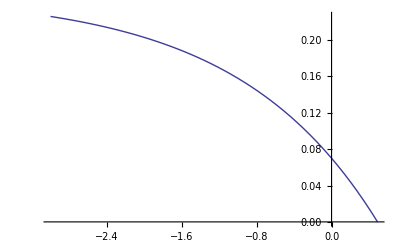

```mathematica
Plot[{FF[I1]/.subst},{I1,-3,0.49}]
```

```mathematica
ParametricPlot
```

ParametricPlot

```mathematica
tabf2=Table[Point[{I1,(sqrtJ2-elips[I1,sqrtJ2,-3]/.subst)}],{I1,-5,0.5,0.1},{sqrtJ2,0,0.3,0.01}];
```

```mathematica
tabf2
```

{{Point[{-5.,-2.13586}],Point[{-5.,-2.12782}],Point[{-5.,-2.1237}],Point[{-5.,-2.1235}],Point[{-5.,-2.12722}],Point[{-5.,-2.13486}],Point[{-5.,-2.14642}],Point[{-5.,-2.1619}],Point[{-5.,-2.18129}],Point[{-5.,-2.20461}],Point[{-5.,-2.23185}],«9»,Point[{-5.,-2.71982}],Point[{-5.,-2.79018}],Point[{-5.,-2.86446}],Point[{-5.,-2.94265}],Point[{-5.,-3.02477}],Point[{-5.,-3.1108}],Point[{-5.,-3.20076}],Point[{-5.,-3.29464}],Point[{-5.,-3.39243}],Point[{-5.,-3.49415}],Point[{-5.,-3.59978}]},«54»,{Point[{0.5,-«18»}],«30»}}

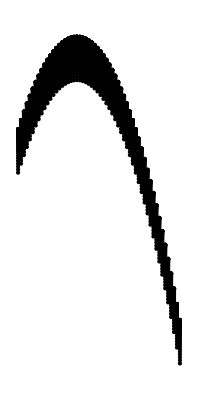

```mathematica
Graphics[tabf2]
```

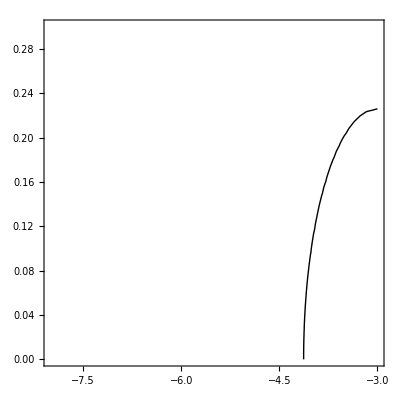

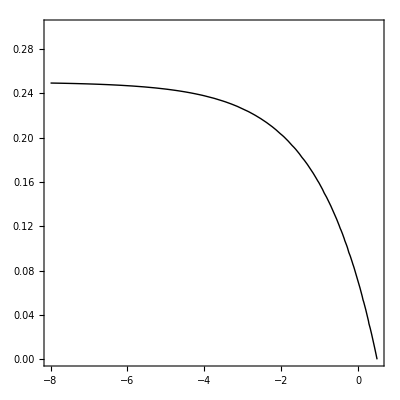

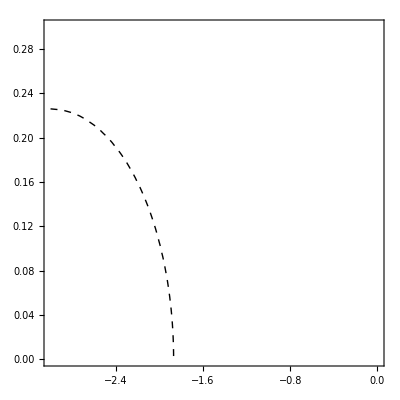

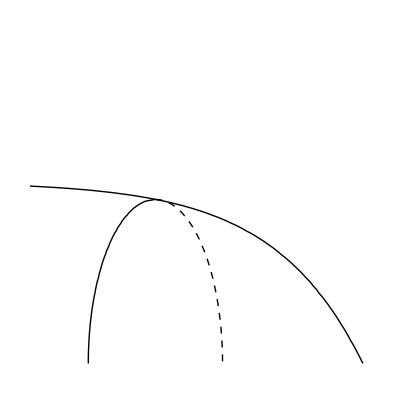

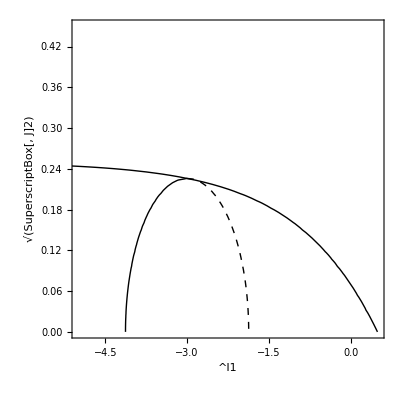

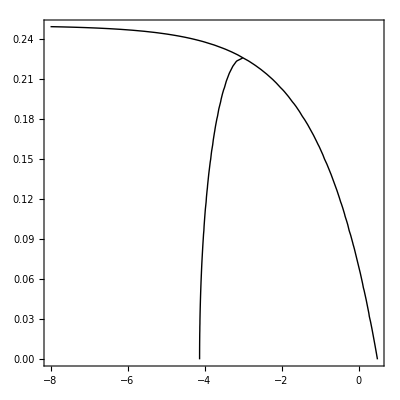

```mathematica
a=ContourPlot[{(elips[I1,sqrtJ2,-3]/.subst)==0},{I1,-8,-3},{sqrtJ2,0,0.3},ContourStyle->{Black,Directive[Black,Thick]}]
b=ContourPlot[{(sqrtJ2-FF[I1]/.subst)==0},{I1,-8,0.5},{sqrtJ2,0,0.3},ContourStyle->{Black,Directive[Black,Thick]}]
c=ContourPlot[{(elips[I1,sqrtJ2,-3]/.subst)==0},{I1,-3,0},{sqrtJ2,0,0.3},ContourStyle->{Black,Directive[Black,Dashed]}]
Show[a,b,c,PlotRange->{{-5,0.5},{0,0.45}},FrameLabel->{"^I1","√(SuperscriptBox[, J]2)"},LabelStyle->Directive[Large],Frame->False]
Show[a,b,c,PlotRange->{{-5,0.5},{0,0.45}},FrameLabel->{"^I1","√(SuperscriptBox[, J]2)"},LabelStyle->Directive[Large]]
Show[a,b,PlotRange->All]
```

```mathematica
elips[-3,0.5,-3]/.subst
```

3.89978

```mathematica
vec=F2[-0.1,Pi/2,beta]/.subst
tab=Table[Point[(vec/.beta->b)],{b,0,2Pi,0.1}]
```

{0.+1/3 (beta+4.97502 (0.25-0.18 ⅇ^(0.67 beta))),-0.0998334 (0.25-0.18 ⅇ^(0.67 beta))+1/3 (beta+4.97502 (0.25-0.18 ⅇ^(0.67 beta))),0.0998334 (0.25-0.18 ⅇ^(0.67 beta))+1/3 (beta+4.97502 (0.25-0.18 ⅇ^(0.67 beta)))}

{Point[{0.116084,0.109095,0.123072}],Point[{0.128732,0.122989,0.134475}],Point[{0.139948,0.135536,0.144359}],Point[{0.14963,0.146642,0.152618}],Point[{0.157674,0.156208,0.159139}],Point[{0.163965,0.164127,0.163802}],Point[{0.168382,0.170285,0.166479}],Point[{0.170795,0.17456,0.167031}],Point[{0.171066,0.176822,0.165311}],Point[{0.169046,0.17693,0.161163}],Point[{0.164576,0.174735,0.154417}],Point[{0.157486,0.170079,0.144894}],Point[{0.147596,0.162791,0.132401}],Point[{0.13471,0.152687,0.116732}],Point[{0.118621,0.139574,0.0976682}],Point[{0.0991073,0.123241,0.0749733}],Point[{0.0759317,0.103468,0.0483958}],Point[{0.0488403,0.0800139,0.0176668}],Point[{0.0175618,0.052625,-0.0175015}],Point[{-0.0181941,0.0210284,-0.0574166}],Point[{-0.0587375,-0.0150676,-0.102407}],Point[{-0.1044,-0.0559747,-0.152826}],Point[{-0.155537,-0.102026,-0.209048}],Point[{-0.212527,-0.153579,-0.271476}],Point[{-0.275777,-0.211014,-0.340539}],Point[{-0.345719,-0.274739,-0.416698}],Point[{-0.422817,-0.345189,-0.500445}],Point[{-0.507568,-0.422831,-0.592305}],Point[{-0.600502,-0.508164,-0.69284}],Point[{-0.702185,-0.601719,-0.802651}],Point[{-0.813224,-0.704067,-0.922382}],Point[{-0.934268,-0.815817,-1.05272}],Point[{-1.06601,-0.937621,-1.1944}],Point[{-1.20919,-1.07017,-1.34821}],Point[{-1.3646,-1.21422,-1.51498}],Point[{-1.53309,-1.37057,-1.69562}],Point[{-1.71557,-1.54005,-1.89109}],Point[{-1.913,-1.72359,-2.10241}],Point[{-2.12642,-1.92216,-2.33069}],Point[{-2.35694,-2.13679,-2.5771}],Point[{-2.60575,-2.36861,-2.84289}],Point[{-2.87411,-2.61881,-3.1294}],Point[{-3.16337,-2.88865,-3.43809}],Point[{-3.47498,-3.1795,-3.77047}],Point[{-3.8105,-3.49281,-4.12819}],Point[{-4.17158,-3.83015,-4.51302}],Point[{-4.55999,-4.19317,-4.92682}],Point[{-4.97763,-4.58366,-5.3716}],Point[{-5.42652,-5.00351,-5.84952}],Point[{-5.90882,-5.45477,-6.36286}],Point[{-6.42685,-5.93961,-6.91409}],Point[{-6.98309,-6.46036,-7.50582}],Point[{-7.58018,-7.0195,-8.14087}],Point[{-8.22096,-7.6197,-8.82223}],Point[{-8.90846,-8.2638,-9.55311}],Point[{-9.6459,-8.95484,-10.337}],Point[{-10.4368,-9.69608,-11.1774}],Point[{-11.2847,-10.491,-12.0785}],Point[{-12.1938,-11.3433,-13.0442}],Point[{-13.1681,-12.257,-14.0792}],Point[{-14.2123,-13.2363,-15.1883}],Point[{-15.3311,-14.2857,-16.3764}],Point[{-16.5298,-15.4102,-17.6493}]}

```mathematica
Graphics3D[tab]
```

-Graphics3D-

```mathematica
f4pts=Table[Point[Rot.(F2[θ,β,sol[[3]]]/.subst)],{θ,Pi/2,Pi/2},{β,0,2Pi,0.07}]
```

{{Point[{0.064292,0.0792761,0.}],Point[{0.064292,0.0790819,0.0055448}],Point[{0.064292,0.0785005,0.0110624}],Point[{0.064292,0.0775345,0.0165259}],Point[{0.064292,0.0761887,0.0219084}],Point[{0.064292,0.0744698,0.0271836}],Point[{0.064292,0.0723861,0.0323257}],Point[{0.064292,0.0699479,0.0373094}],Point[{0.064292,0.0671671,0.0421104}],Point[{0.064292,0.0640573,0.0467051}],Point[{0.064292,0.0606337,0.0510711}],Point[{0.064292,0.0569132,0.0551869}],Point[{0.064292,0.0529138,0.0590324}],Point[{0.064292,0.0486554,0.0625888}],Point[{0.064292,0.0441586,0.0658386}],Point[{0.064292,0.0394455,0.0687659}],Point[{0.064292,0.0345392,0.0713564}],Point[{0.064292,0.0294637,0.0735975}],Point[{0.064292,0.024244,0.075478}],Point[{0.064292,0.0189055,0.0769889}],Point[{0.064292,0.0134743,0.0781226}],Point[{0.064292,0.00797722,0.0788737}],Point[{0.064292,0.00244103,0.0792385}],Point[{0.064292,-0.00310712,0.0792152}],Point[{0.064292,-0.00864004,0.0788039}],Point[{0.064292,-0.0141307,0.0780066}],Point[{0.064292,-0.019552,0.0768272}],Point[{0.064292,-0.0248777,0.0752715}],Point[{0.064292,-0.0300815,0.0733472}],Point[{0.064292,-0.0351379,0.0710635}],Point[{0.064292,-0.0400222,0.0684319}],Point[{0.064292,-0.0447105,0.065465}],Point[{0.064292,-0.0491798,0.0621775}],Point[{0.064292,-0.0534083,0.0585855}],Point[{0.064292,-0.0573751,0.0547065}],Point[{0.064292,-0.0610609,0.0505595}],Point[{0.064292,-0.0644477,0.0461649}],Point[{0.064292,-0.0675187,0.0415442}],Point[{0.064292,-0.0702591,0.03672}],Point[{0.064292,-0.0726553,0.0317159}],Point[{0.064292,-0.0746957,0.0265566}],Point[{0.064292,-0.0763702,0.0212671}],Point[{0.064292,-0.0776707,0.0158735}],Point[{0.064292,-0.0785907,0.0104021}],Point[{0.064292,-0.0791258,0.00487974}],Point[{0.064292,-0.0792733,-0.000666494}],Point[{0.064292,-0.0790325,-0.00620946}],Point[{0.064292,-0.0784047,-0.011722}],Point[{0.064292,-0.0773928,-0.0171772}],Point[{0.064292,-0.0760018,-0.0225482}],Point[{0.064292,-0.0742386,-0.0278087}],Point[{0.064292,-0.0721118,-0.0329331}],Point[{0.064292,-0.0696318,-0.0378961}],Point[{0.064292,-0.0668107,-0.0426736}],Point[{0.064292,-0.0636623,-0.047242}],Point[{0.064292,-0.0602022,-0.051579}],Point[{0.064292,-0.0564472,-0.0556634}],Point[{0.064292,-0.0524157,-0.0594752}],Point[{0.064292,-0.0481274,-0.0629956}],Point[{0.064292,-0.0436035,-0.0662075}],Point[{0.064292,-0.038866,-0.0690951}],Point[{0.064292,-0.0339381,-0.0716443}],Point[{0.064292,-0.028844,-0.0738426}],Point[{0.064292,-0.0236086,-0.0756792}],Point[{0.064292,-0.0182575,-0.0771451}],Point[{0.064292,-0.0128171,-0.0782331}],Point[{0.064292,-0.00731382,-0.078938}],Point[{0.064292,-0.00177476,-0.0792562}],Point[{0.064292,0.00377299,-0.0791863}],Point[{0.064292,0.00930226,-0.0787284}],Point[{0.064292,0.014786,-0.077885}],Point[{0.064292,0.0201973,-0.0766601}],Point[{0.064292,0.0255096,-0.0750597}],Point[{0.064292,0.030697,-0.0730917}],Point[{0.064292,0.0357341,-0.0707656}],Point[{0.064292,0.0405961,-0.068093}],Point[{0.064292,0.0452593,-0.0650868}],Point[{0.064292,0.0497009,-0.0617618}],Point[{0.064292,0.0538989,-0.0581344}],Point[{0.064292,0.057833,-0.0542222}],Point[{0.064292,0.0614838,-0.0500444}],Point[{0.064292,0.0648335,-0.0456214}],Point[{0.064292,0.0678656,-0.0409751}],Point[{0.064292,0.0705653,-0.036128}],Point[{0.064292,0.0729194,-0.031104}],Point[{0.064292,0.0749163,-0.0259276}],Point[{0.064292,0.0765463,-0.0206243}],Point[{0.064292,0.0778014,-0.0152199}],Point[{0.064292,0.0786754,-0.00974097}],Point[{0.064292,0.079164,-0.00421434}]}}

```mathematica
subst1 = {D->  0.67,R-> 2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->1,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
pts1=Table[Point[(F2[θ,β,sol[[3]]]/.subst1)],{θ,Pi/2,Pi/2},{β,0,2Pi,0.007}];
subst2 = {D->  0.67,R-> 2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->7/9,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
pts2=Table[Point[(F2[θ,β,sol[[3]]]/.subst2)],{θ,Pi/2,Pi/2},{β,0,2Pi,0.007}];
subst3 = {D->  0.67,R-> 2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->9/7,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
pts3=Table[Point[(F2[θ,β,sol[[3]]]/.subst3)],{θ,Pi/2,Pi/2},{β,0,2Pi,0.007}];

subst1 = {D->  0.67,R-> 2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->1,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
pts11=Table[Point[Rot.(F2[θ,β,sol[[3]]]/.subst1).Transpose[Rot]],{θ,Pi/2,Pi/2},{β,0,2Pi,0.007}];
subst2 = {D->  0.67,R-> 2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->7/9,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
pts22=Table[Point[(Rot.F2[θ,β,sol[[3]]]/.subst2).Transpose[Rot]],{θ,Pi/2,Pi/2},{β,0,2Pi,0.007}];
subst3 = {D->  0.67,R-> 2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->9/7,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
pts33=Table[Point[(Rot.F2[θ,β,sol[[3]]]/.subst3).Transpose[Rot]],{θ,Pi/2,Pi/2},{β,0,2Pi,0.007}];

subst1 = {D->  0.67,R-> 2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->1,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
pts111=Table[Point[(F2[θ,β,sol[[3]]]/.subst1)],{θ,Pi/2,Pi/2},{β,0,2Pi,0.007}];
subst2 = {D->  0.67,R-> 2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->7/9,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
pts222=Table[Point[(F2[θ,β,sol[[3]]]/.subst2)],{θ,Pi/2,Pi/2},{β,0,2Pi,0.007}];
subst3 = {D->  0.67,R-> 2.5(*5.3307429045*),A->  0.25,B->  0.67,C-> 0.18,W->  0.066,ψ->9/7,NN->0,ϕ->0,G->40,K->66.6667,d-> 0.67};
pts333=Table[Point[(F2[θ,β,sol[[3]]]/.subst3)],{θ,Pi/2,Pi/2},{β,0,2Pi,0.007}];
```

```mathematica
(*gph11=Graphics3D[{PointSize[Large],pts11,pts22,pts33}];
Show[gph11,Boxed->True]
gph111=Graphics3D[{PointSize[Large],pts111,pts222,pts333}];
Show[gph111,graph2cart]*)
gph1=Graphics3D[{PointSize[Large],pts1,pts2,pts3}]
Show[gph1]
(*gph1=Graphics3D[{PointSize[Large],pts1,pts2,pts3}];
Show[gph1,graph1sigs]*)
```

-Graphics3D-

-Graphics3D-

```mathematica
Graphics3D[{pts1,pts2,pts3},Boxed->False]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-